E(κ_0a) plots with fixed a

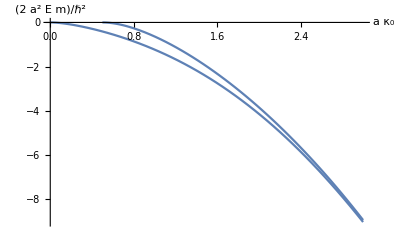

```mathematica
Quiet[
p1 = Plot[-(y/.Solve[Reduce[{y/x==1+Exp[-2*y]}, y]/.C[1]->0, y])^2, {x, 0, 3}, AxesLabel->{Subscript[κ, 0]*a, 2*m*a^2"E"/ℏ^2}, ImageSize->Full];
p2 = Plot[-(y/.Solve[Reduce[{y/x==1-Exp[-2*y]}, y]/.C[1]->0, y][[1]])^2, {x, 0.5, 3}];
]
Show[p1, p2]
```

E(κ_0a) plots with fixed κ_0

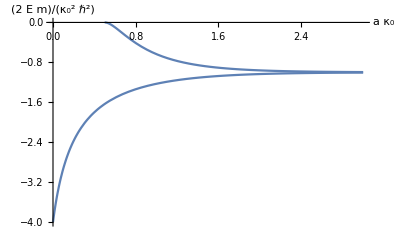

```mathematica
Quiet[
p1 = Plot[-(y/.Solve[Reduce[{y/x==1+Exp[-2*y]}, y]/.C[1]->0, y])^2/x^2, {x, 0, 3}, AxesLabel->{Subscript[κ, 0]*a, 2*m*"E"/ℏ^2/Subscript[κ, 0]^2}, ImageSize->Full, PlotRange->{-4, 0}];
p2 = Plot[-(y/.Solve[Reduce[{y/x==1-Exp[-2*y]}, y]/.C[1]->0, y][[1]])^2/x^2, {x, 0.5, 3}];
]
Show[p1, p2]
```

Absolute value of ψ-function

```mathematica
B=.;A=B*(1+Exp[-2*k*a]);
even = Piecewise[{
{B*(Exp[-k*(x+a)]+Exp[k*(x-a)]), -a<x≤ a},
{A*Exp[-k*(x-a)],x>a},
{A*Exp[k*(x+a)],x<-a}}]
```

Piecewise[{{B (ⅇ^(k (-a+x))+ⅇ^(-k (a+x))), -a<x≤a}, {B ⅇ^(-k (-a+x)) (1+ⅇ^(-2 a k)), x>a}, {B ⅇ^(k (a+x)) (1+ⅇ^(-2 a k)), x<-a}, {0, True}}]

```mathematica
Assuming [a>0&&k>0&&Subscript[k, 0]>0,
evenint = FullSimplify[Integrate[even^2, {x, -∞, ∞}]]
]
```

(2 B^2 ⅇ^(-2 a k) (1+ⅇ^(2 a k)+2 a k))/k

```mathematica
FullSimplify[(B/.Solve[evenint==1,B][[2]])]
```

(ⅇ^(a k) √k)/(√2 √(1+ⅇ^(2 a k)+2 a k))

```mathematica
B=.;A=B*(1-Exp[-2*k*a]);
uneven = Piecewise[{
{B*(Exp[-k*(x+a)]-Exp[k*(x-a)]), -a<x≤ a},
{A*Exp[-k*(x-a)],x>a},
{-A*Exp[k*(x+a)],x<-a}}]
```

Piecewise[{{B (-ⅇ^(k (-a+x))+ⅇ^(-k (a+x))), -a<x≤a}, {B ⅇ^(-k (-a+x)) (1-ⅇ^(-2 a k)), x>a}, {-B ⅇ^(k (a+x)) (1-ⅇ^(-2 a k)), x<-a}, {0, True}}]

```mathematica
Assuming [a>0&&k>0&&Subscript[k, 0]>0,
unevenint = FullSimplify[Integrate[uneven^2, {x, -∞, ∞}]]
]
```

(2 B^2 ⅇ^(-2 a k) (-1+ⅇ^(2 a k)-2 a k))/k

```mathematica
FullSimplify[(B/.Solve[unevenint==1,B][[2]])]
```

(ⅇ^(a k) √k)/(√2 √(-1+ⅇ^(2 a k)-2 a k))

```mathematica
left [x_]:=Sqrt[Subscript[k, 0]]*Exp[-Subscript[k, 0]*Abs[x+a]]
A=.;B=.;
Assuming [a>0&&k>0&&Subscript[k, 0]>0,
FullSimplify[Integrate[A*Exp[k*(x+a)]*left[x], {x, -∞, -a}]]
]
```

(A √k_0)/(k+k_0)